## Approximate GinOE ypotential

```mathematica
fun=-Log[Erfc[y √2] Exp[2 y^2]]
```

-Log[ⅇ^(2 y^2) Erfc[√2 y]]

```mathematica
zlist=Range[4,18];
getLoss[expr_]:=Block[{$MaxExtraPrecision=500},√(Sum[N[((fun-expr)/.y->z),50]^2,{z,zlist}]/Length[zlist])]
```

```mathematica
ClearAll[a];
fapprox0=-Log[1/(√(2 π) y)]+a;
sol=Solve[(fun-fapprox0-PadeApproximant[fun-fapprox0,{y,∞,{6,8}}]==0)/.y->4,a];
a=N[a/.sol[[1,1]],500];
fapprox1=N[fapprox0+PadeApproximant[fun-fapprox0,{y,∞,{6,8}}],40]
```

0.890451959047853643013774438288428111531+(-0.890451959047853643013774438288428111531-9.869261681191832701731724404616295971553/y^6-16.90359050157721106889984300899829825369/y^4-7.423694049765192486628066963007045221308/y^2)/(1.+2.174258030977644555812272331973294792748/y^8+15.74732873975124317572963943709831902318/y^6+21.22717377517984141370472593958542366059/y^4+8.617751886323607565086681753902613859088/y^2)-1. Log[0.3989422804014326779399460599343818684759/y]

```mathematica
getLoss[fapprox1]
```

1.8976572503953882177891346×10^-14

```mathematica
Max[Table[Abs[fun-fapprox1]/.y->yi,{yi,4,18,1/1000}]]
```

2.3797382109666735397048774×10^-13

```mathematica
?Table
```

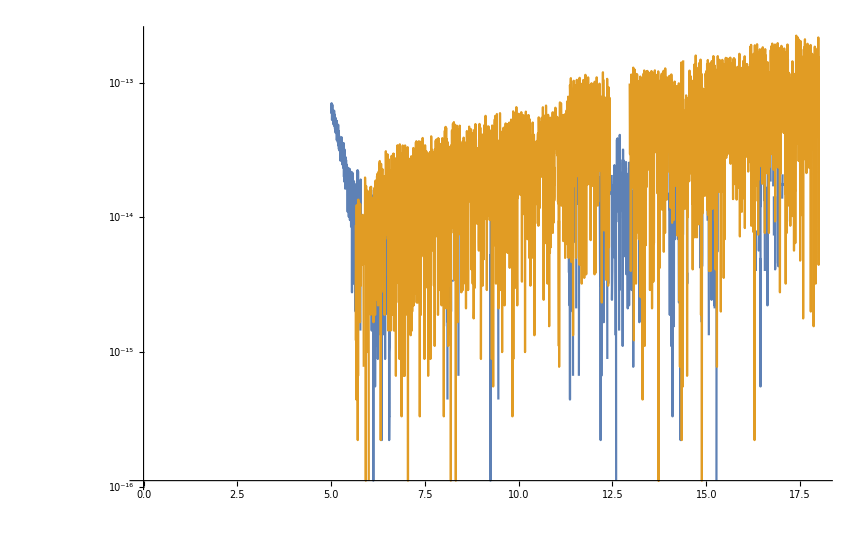

```mathematica
expr=fapprox1-fun;
LogPlot[{expr,-expr},{y,5,18},AxesOrigin->{0,0},PlotRange->Full]
```

## Integrate the proposal ellipse

```mathematica
Solve[√(semiaxisx^2 - (scale y)^2)-offset==0&&y>0,y,Assumptions->{offset < semiaxisx,scale>0,offset>0}]
```

{{y→ConditionalExpression[(√(-offset^2+semiaxisx^2))/scale, semiaxisx>0&&offset<semiaxisx]}}

```mathematica
ymax=(√(-offset^2+semiaxisx^2))/scale;
Integrate[√(semiaxisx^2 - (scale y)^2)-offset,{y,0,a},Assumptions->{offset < semiaxisx,scale>0,offset>0, 0>a, a<ymax}]
```

ConditionalExpression[-a offset+(a scale √(-a^2 scale^2+semiaxisx^2)+semiaxisx^2 ArcTan[(a scale)/(√(-a^2 scale^2+semiaxisx^2))])/(2 scale), a scale+semiaxisx≥0]

## TwoPointPade

```mathematica
ClearAll[f,x,y,x1,a,b];
f=I1f[x];
x1=1/x;
p1=1;
n1=1;
p2=∞;
n2=5;
nnum=5;
nden=5;
res=Sum[a[j] x1^j,{j,0,nnum}]/Sum[b[j] x1^j,{j,0,nden}];
eqns1=CoefficientList[Normal[Series[f-res,{x,p1,n1}]],x];
eqns2=CoefficientList[Normal[Series[(f-res),{x,p2,n2}]]/.x->1/y,y];
eqns=Table[e==0,{e,Join[eqns1,eqns2,{b[0]-1}]}];
coeffs=Flatten[{Table[a[j],{j,0,nnum}],Table[b[j],{j,0,nden}]}];
Print[{eqns,coeffs}];
sol=Solve[eqns,coeffs];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{2+(-a[1]-2 a[2]-3 a[3]-4 a[4]-5 a[5])/(b[0]+b[1]+b[2]+b[3]+b[4]+b[5])-(a[0]+a[1]+a[2]+a[3]+a[4]+a[5])/(b[0]+b[1]+b[2]+b[3]+b[4]+b[5])+((a[0]+a[1]+a[2]+a[3]+a[4]+a[5]) (b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]))/(b[0]+b[1]+b[2]+b[3]+b[4]+b[5])^2-(√(2/(ⅇ π)))/Erfc[1/(√2)]+1/2 (-1+Log[2]-Log[π]-2 Log[Erfc[1/(√2)]])==0,-2-(-a[1]-2 a[2]-3 a[3]-4 a[4]-5 a[5])/(b[0]+b[1]+b[2]+b[3]+b[4]+b[5])-((a[0]+a[1]+a[2]+a[3]+a[4]+a[5]) (b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]))/(b[0]+b[1]+b[2]+b[3]+b[4]+b[5])^2+(√(2/(ⅇ π)))/Erfc[1/(√2)]==0,-a[0]/b[0]==0,(-a[1] b[0]+a[0] b[1])/b[0]^2==0,1+(-a[2] b[0]^2+a[1] b[0] b[1]-a[0] b[1]^2+a[0] b[0] b[2])/b[0]^3==0,-a[3]/b[0]+(a[2] b[1])/b[0]^2-(a[1] (b[1]^2-b[0] b[2]))/b[0]^3-(a[0] (-b[1]^3+2 b[0] b[1] b[2]-b[0]^2 b[3]))/b[0]^4==0,-5/2-a[4]/b[0]+(a[3] b[1])/b[0]^2-(a[2] (b[1]^2-b[0] b[2]))/b[0]^3-(a[1] (-b[1]^3+2 b[0] b[1] b[2]-b[0]^2 b[3]))/b[0]^4-(a[0] (b[1]^4-3 b[0] b[1]^2 b[2]+b[0]^2 b[2]^2+2 b[0]^2 b[1] b[3]-b[0]^3 b[4]))/b[0]^5==0,-a[5]/b[0]+(a[4] b[1])/b[0]^2-(a[3] (b[1]^2-b[0] b[2]))/b[0]^3-(a[2] (-b[1]^3+2 b[0] b[1] b[2]-b[0]^2 b[3]))/b[0]^4-(a[1] (b[1]^4-3 b[0] b[1]^2 b[2]+b[0]^2 b[2]^2+2 b[0]^2 b[1] b[3]-b[0]^3 b[4]))/b[0]^5-(a[0] (-b[1]^5+4 b[0] b[1]^3 b[2]-3 b[0]^2 b[1] b[2]^2-3 b[0]^2 b[1]^2 b[3]+2 b[0]^3 b[2] b[3]+2 b[0]^3 b[1] b[4]-b[0]^4 b[5]))/b[0]^6==0,-1+b[0]==0},{a[0],a[1],a[2],a[3],a[4],a[5],b[0],b[1],b[2],b[3],b[4],b[5]}}

```mathematica
sol={};
vars=coeffs;
getVars[eqns_, vars_]:=Table[Cases[vars,_?(Function[v,!FreeQ[e,v]])],{e,eqns}];
ClearAll[reduce,myAssert];
SetAttributes[myAssert,HoldAll];
myAssert[test_,msg_]:=If[Not[test],Message[reduce::assert,msg];
Return[$Failed,Module]];
reduce[i_,v_]:=Module[{eq,curSol,prevLen},
eq=eqns[[i]];
curSol=Solve[eq,v];
MyAssert[Length[curSol]==1,"Length[curSol] should be 1"];
sol=Join[sol,curSol[[1]]];
prevLen=Length[vars];
vars=Cases[vars,Except[v]];
MyAssert[Length[vars]==prevLen-1,"Length[vars] should be decreased by one!"];
eqns=Delete[eqns,i]/.sol;
];
```

```mathematica
evars=getVars[eqns,vars];
Table[{i,Length[evars[[i]]]},{i,1,Length[evars]}]
```

{{1,12},{2,12},{3,2},{4,4},{5,6},{6,8},{7,10},{8,12},{9,1}}

```mathematica
eqns[[3]]
```

-a[0]/b[0]-Log[1+(ⅇ^(1/(2 y^2)) √(π/2))/y+((-1)^(1+Floor[(π+2 Arg[y])/(2 π)]) ⅇ^(1/(2 y^2)) √(π/2))/y-y^2+3 y^4]==0

```mathematica
reduce[3,evars[[3]][[1]]]
```

```mathematica
Length[vars]
```

10

```mathematica
vars
```

{a[1],a[2],a[3],a[4],a[5],b[1],b[2],b[3],b[4],b[5]}

```mathematica
Length[Union@@evars]
```

11

```mathematica
Length[Union[evars]]
```

6

```mathematica
Length[eqns]
```

8

```mathematica
Table[{i,Length[Variables[eqns[[i]]]]},{i,1,Length[eqns]}]
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0}}

```mathematica
eqns={a[0]==b[1]^2,b[2]==0};
vars={a[0],a[1],a[2],b[0],b[1],b[2]};

eqnVars=Table[Cases[vars,_?(Function[v,!FreeQ[e,v]])],{e,eqns}]
```

{{a[0],b[1]},{b[2]}}

```mathematica
Length[eqns]
```

9

```mathematica
Length[coeffs]
```

12

```mathematica
res/.x->1
```

(a[0]+x1 a[1]+x1^2 a[2]+x1^3 a[3]+x1^4 a[4]+x1^5 a[5])/(b[0]+x1 b[1]+x1^2 b[2]+x1^3 b[3]+x1^4 b[4]+x1^5 b[5])

```mathematica
eqns1[[2]]
```

-2+(√(2/(ⅇ π)))/Erfc[1/(√2)]

```mathematica
res/.x->1
```

(a[0]+x1 a[1]+x1^2 a[2]+x1^3 a[3]+x1^4 a[4]+x1^5 a[5])/(b[0]+x1 b[1]+x1^2 b[2]+x1^3 b[3]+x1^4 b[4]+x1^5 b[5])/.{}⟦1⟧

```mathematica
Clear[twoPointPade];
twoPointPade[f_,{x_,{p1_,n1_},{Infinity,n2_},{nnum_,nden_}}]:=Module[{res,a,b,eqns1,eqns2,eqns,p2=Infinity,sol,polyNum,polyDen,x1=1/x,y,coeffs},
res=Sum[a[j] x1^j,{j,0,nnum}]/Sum[b[j] x1^j,{j,0,nden}];
eqns1=CoefficientList[Normal[Series[f-res,{x,p1,n1}]],x];
eqns2=CoefficientList[Normal[Series[(f-res),{x,p2,n2}]]/.x->1/y,y];
eqns=Table[e==0,{e,Join[eqns1,eqns2,{b[0]-1}]}];
coeffs=Flatten[{Table[a[j],{j,0,nnum}],Table[b[j],{j,0,nden}]}];
Print[{Length[eqns],Length[coeffs]}];
sol=Solve[eqns,coeffs];
res=res/.sol[[1]];
res
];
```

```mathematica
(*Define a test function*)testFunc[x_]:=I1f[x];

(*Compute the two-point Pade approximant*)
pade=twoPointPade[testFunc[x],{x,{1,1},{Infinity,5},{3,4}}];
Print[pade]

(*Check how well the Pade approximant matches the original function*)
(*Plot[{testFunc[x],pade},{x,-10,10},PlotLegends->"Expressions"];*)
```

{9,9}

(1/x^2+(2 (-4 √(2/(ⅇ π))-5 Erfc[1/(√2)]+22 Erfc[1/(√2)] Log[2]-9 Erfc[1/(√2)] Log[2]^2-22 Erfc[1/(√2)] Log[π]+18 Erfc[1/(√2)] Log[2] Log[π]-9 Erfc[1/(√2)] Log[π]^2-44 Erfc[1/(√2)] Log[Erfc[1/(√2)]]+36 Erfc[1/(√2)] Log[2] Log[Erfc[1/(√2)]]-36 Erfc[1/(√2)] Log[π] Log[Erfc[1/(√2)]]-36 Erfc[1/(√2)] Log[Erfc[1/(√2)]]^2))/(x^3 (8 √(2/(ⅇ π))-Erfc[1/(√2)]-26 Erfc[1/(√2)] Log[2]+11 Erfc[1/(√2)] Log[2]^2+26 Erfc[1/(√2)] Log[π]-22 Erfc[1/(√2)] Log[2] Log[π]+11 Erfc[1/(√2)] Log[π]^2+52 Erfc[1/(√2)] Log[Erfc[1/(√2)]]-44 Erfc[1/(√2)] Log[2] Log[Erfc[1/(√2)]]+44 Erfc[1/(√2)] Log[π] Log[Erfc[1/(√2)]]+44 Erfc[1/(√2)] Log[Erfc[1/(√2)]]^2)))/(1+5/(2 x^2)+(5 (-4 √(2/(ⅇ π))-5 Erfc[1/(√2)]+22 Erfc[1/(√2)] Log[2]-9 Erfc[1/(√2)] Log[2]^2-22 Erfc[1/(√2)] Log[π]+18 Erfc[1/(√2)] Log[2] Log[π]-9 Erfc[1/(√2)] Log[π]^2-44 Erfc[1/(√2)] Log[Erfc[1/(√2)]]+36 Erfc[1/(√2)] Log[2] Log[Erfc[1/(√2)]]-36 Erfc[1/(√2)] Log[π] Log[Erfc[1/(√2)]]-36 Erfc[1/(√2)] Log[Erfc[1/(√2)]]^2))/(x^3 (8 √(2/(ⅇ π))-Erfc[1/(√2)]-26 Erfc[1/(√2)] Log[2]+11 Erfc[1/(√2)] Log[2]^2+26 Erfc[1/(√2)] Log[π]-22 Erfc[1/(√2)] Log[2] Log[π]+11 Erfc[1/(√2)] Log[π]^2+52 Erfc[1/(√2)] Log[Erfc[1/(√2)]]-44 Erfc[1/(√2)] Log[2] Log[Erfc[1/(√2)]]+44 Erfc[1/(√2)] Log[π] Log[Erfc[1/(√2)]]+44 Erfc[1/(√2)] Log[Erfc[1/(√2)]]^2))+(2 (-4 √(2/(ⅇ π))-5 Erfc[1/(√2)]+22 Erfc[1/(√2)] Log[2]-9 Erfc[1/(√2)] Log[2]^2-22 Erfc[1/(√2)] Log[π]+18 Erfc[1/(√2)] Log[2] Log[π]-9 Erfc[1/(√2)] Log[π]^2-44 Erfc[1/(√2)] Log[Erfc[1/(√2)]]+36 Erfc[1/(√2)] Log[2] Log[Erfc[1/(√2)]]-36 Erfc[1/(√2)] Log[π] Log[Erfc[1/(√2)]]-36 Erfc[1/(√2)] Log[Erfc[1/(√2)]]^2))/(x (8 √(2/(ⅇ π))-Erfc[1/(√2)]-26 Erfc[1/(√2)] Log[2]+11 Erfc[1/(√2)] Log[2]^2+26 Erfc[1/(√2)] Log[π]-22 Erfc[1/(√2)] Log[2] Log[π]+11 Erfc[1/(√2)] Log[π]^2+52 Erfc[1/(√2)] Log[Erfc[1/(√2)]]-44 Erfc[1/(√2)] Log[2] Log[Erfc[1/(√2)]]+44 Erfc[1/(√2)] Log[π] Log[Erfc[1/(√2)]]+44 Erfc[1/(√2)] Log[Erfc[1/(√2)]]^2))+(Erfc[1/(√2)] (-11+7 Log[2]-7 Log[π]-14 Log[Erfc[1/(√2)]])^2)/(x^4 (16 √(2/(ⅇ π))-2 Erfc[1/(√2)]-52 Erfc[1/(√2)] Log[2]+22 Erfc[1/(√2)] Log[2]^2+52 Erfc[1/(√2)] Log[π]-44 Erfc[1/(√2)] Log[2] Log[π]+22 Erfc[1/(√2)] Log[π]^2+104 Erfc[1/(√2)] Log[Erfc[1/(√2)]]-88 Erfc[1/(√2)] Log[2] Log[Erfc[1/(√2)]]+88 Erfc[1/(√2)] Log[π] Log[Erfc[1/(√2)]]+88 Erfc[1/(√2)] Log[Erfc[1/(√2)]]^2)))

```mathematica
Module[{pade1,x1},
pade1=pade/.x->x1;
I3f[y_]:=pade1/.x1->y
];
```

## Sampling truncated normal

We want to sample x1 from the standard normal distribution conditioned on x1>x0 for some x0 between 0 and 100.
The pdf (as a differential form) is I[x1>x0] c1 √(2/π)Exp[-x1^2/2]ⅆx1 where
* c1 can be determined from the normalization condition,
* I[a] is the indicator function: 1 if a is True and 0 otherwise.

Let f2[x0]=(∫_x0)^∞√(2/π)Exp[-x^2/2]ⅆx and x2=f2[x1]. Now the pdf of x2 is simply I[x2 < f2[x0]] c1 ⅆ x2 and x2 can be sampled from (0, f2[x0]).

```mathematica
Module[{x,x0,x0s,f2I},
f2I=Integrate[√(2/π)Exp[-x^2/2],{x,x0, ∞}, Assumptions->x0 > 0];
f2[x0s_]:=f2I/.x0->x0s;
];
Print["f2[x]=",f2[x]]
```

f2[x]=Erfc[x/(√2)]

However, f2[100] wouldn't fit into float64 (aka double aka FP64):

```mathematica
N[{f2[5],f2[100]},40]
```

{5.733031437583878233475046657492907077088×10^-7,2.688358153488396610146160334270505693246×10^-2174}

Thus, for x0 = 100 the interval for x2 is so small that none of its values can represented as a valid float64 number. Thus, we need a different approach. Let's define f3[x]=-Log[f2[x]] and x3 = f3[x1]. Then x2 = Exp[-x3] and pdf of I[x3 > f3[x0]] Exp[-(x3-f3[x0])] ⅆx3, i.e. x3-f3[x0] can be sampled from exponential distribution, i.e. the sampling procedure is the following:
1. Compute x3min = f3[x0]
2. Sample dx3 from exponential distribution
3. Compute x3 = x3min + dx3
4. Return x1 = f3i[x3], where f3i is the inverse function of f3.

```mathematica
Module[{x,x3,x3s,f3iSol,f3iI},
f3[x_]:=-Log[f2[x]];
f3iSol=Solve[f3[x]==x3&&x>0,{x},Assumptions->x3>0];
Print[f3iSol];
f3iI=x/.f3iSol[[1]];
f3i[x3s_]:=f3iI/.x3->x3s;
];
Print[f3i[x]];
```

{{x$63324→√2 InverseErfc[ⅇ^-x3$63324]}}

√2 InverseErfc[ⅇ^-x]

Two remaining challenges are to compute f3 and f3i numerically. We can use standard formulas for small x (e.g. x0, x1 < 5; x3min, x3 < 14), but using them for large x has issues:

```mathematica
Print["f3[100]: ",f3[100.0]," (machine precision) vs ",N[f3[100],50]," (precise)."]
Print["f3i[5000.0]: ",f3i[5005.0]," (machine precision) vs ",N[f3i[5005],50]," (precise)."]
```

f3[100]: Indeterminate (machine precision) vs 5004.8310615136451433168852252085673547718388678343 (precise).

General::munfl: Exp[-5005.] is too small to represent as a normalized machine number; precision may be lost.

f3i[5000.0]: ∞ (machine precision) vs 100.00168920171155828390374555156283792174323821621 (precise).

In order to find good numerical algorithms for f3 and f3i we rewrite f3 as f3[x] = x^2/2 + Log[x] - Log[√(2/π)]-Log[(∫_0)^∞Exp[-z]/(√(1+(2z)/x^2))ⅆz] and let f4[x] be the last term in this expression:

```mathematica
f4[x_]:=-Log[Integrate[Exp[-z]/(√(1+(2z)/x^2)),{z,0,∞},Assumptions->x>0]];
f4V2[x_]:=-x^2/2-1/2 Log[π/2] -Log[x]-Log[ Erfc[x/(√2)]];(*For some reason V2 works with arbitrary precision computations better*)
{Simplify[f3[x]==x^2/2+Log[x]-Log[√(2/π)]+f4[x],Assumptions->x>0],Simplify[f4[x]==f4V2[x],Assumptions->x>0]}
```

{True,True}

Our first task is to find an approximation for f4:

Time: 0.121867s

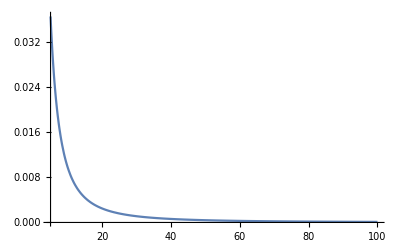

```mathematica
f4N[x_?NumericQ]:=Module[{xN=SetPrecision[x,100]},N[f4V2[xN],100]];
res=Timing[Plot[f4N[x],{x,5,100},WorkingPrecision->100,PlotRange->All]];
Print["Time: ",res[[1]],"s"];
res[[2]]
```

```mathematica
numA=4;
numB=5;
f4Ansatz=Sum[a[i] x^(-2 i),{i,1,numA}]/(1 + Sum[b[i] x^(-2 i),{i,1,numB}]);
xmin=5;
xmax=100;
nPoints=1600;
xData=Range[xmin,xmax,(xmax-xmin)/(nPoints - 1)];
yData=f4N/@xData;
data=Transpose[{xData,yData}];
(*
pade=PadeApproximant[f4[√xp2],{xp2,∞,{numA,numB}}];
padeCoeffs={
CoefficientList[Numerator[pade]/.xp2->1/xp2i,xp2i],
CoefficientList[Denominator[pade]/.xp2->1/xp2i,xp2i]};
Print[Length[padeCoeffs[[1]]==3],Length[padeCoeffs[[2]]==4]];
Print[padeCoeffs];
padeCoeffs=Join[Drop[padeCoeffs⟦1⟧,1],Drop[padeCoeffs⟦2⟧,1]];
coeffVars=Join[Table[a[i],{i,1,numA}],Table[b[i],{i,1,numB}]];
startingValues=Thread[coeffVars->padeCoeffs];
(*No way to provide starting values in NonLinearModelFit?*)
*)
fit=NonlinearModelFit[data,f4Ansatz,coeffVars,x,WorkingPrecision->100];
```

NonlinearModelFit::precw: The precision of the data and model function (81.7726) is less than the specified WorkingPrecision (100).

```mathematica
fit["BestFitParameters"]
```

FittedModel::precw: The precision of the argument function (81.7726) is less than WorkingPrecision (100).

{a[1]→0.9999999999982223233800324512864557397551351311247411198699225654497020191671371765163912906704024091,a[2]→31.65914337015056937390433489848462353083134696261088935371272999867626731109249021456155302079374855,a[3]→273.490498082387894692390001388513921355014936860497551007302871706177796521075454241004722464288864,a[4]→596.921392509356213359199409986892363696045166813043552056846242064165374172705051394262952039438392,b[1]→34.15914336669095062081094728117717787813430205775482891566644721734346321600346439102427067406350153,b[2]→346.5550251709101101267307009030179360713609304426691004315412290657901028637051282082744396873508994,b[3]→1130.262314385566482582497153183173744689343945721864642863150167694265160838135915154847460744970549,b[4]→749.9034979643479523821218177815402054374417844266005347525420049629544596225138558666839789293451896,b[5]→-169.399064806894676575293456855681226104580897571357559578655494556533173932998493461701960309843212}

```mathematica
f4N[x]-(f4Ansatz/.fit["BestFitParameters"])/.x->5
```

-9.24427232706887866437896979127609593138899304825226464478916295697×10^-17

FittedModel::precw: The precision of the argument function (81.7726) is less than WorkingPrecision (100).

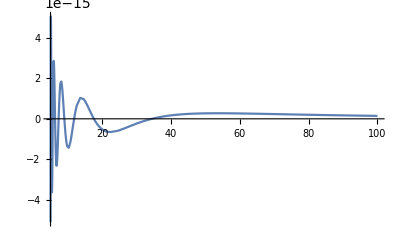

```mathematica
Plot[{f4N[x]-(f4Ansatz/.fit["BestFitParameters"])},{x,5,100},WorkingPrecision->100,PlotRange->All]
```

```mathematica
seriesPythonForm[coeffs_,x_]:=Module[{res,coeffs2},
res=coeffs[[-1]];
coeffs2=Drop[coeffs,-1];
While[Length[coeffs2]>0,res=res x+coeffs2[[-1]]; coeffs2=Drop[coeffs2,-1];];
res
];
Module[{f4fit,xm2},
f4fit=seriesPythonForm[Join[{0},Table[N[a[i]/.fit["BestFitParameters"],18],{i,1,numA}]],xm2]/seriesPythonForm[Join[{1},Table[N[b[i]/.fit["BestFitParameters"],18],{i,1,numB}]],xm2];
Print[f4fit];
f4Approx[x_]:=f4fit/.xm2->x^-2;
];
```

FittedModel::precw: The precision of the argument function (81.7726) is less than WorkingPrecision (100).

General::stop: Further output of FittedModel::precw will be suppressed during this calculation.

(xm2$3932998 (0.999999999998222323+xm2$3932998 (31.6591433701505694+xm2$3932998 (273.490498082387895+596.921392509356213 xm2$3932998))))/(1+xm2$3932998 (34.1591433666909506+xm2$3932998 (346.55502517091011+xm2$3932998 (1130.26231438556648+(749.903497964347952-169.399064806894677 xm2$3932998) xm2$3932998))))

```mathematica
{f4N[x],f4Approx[x],f4N[x]-f4Approx[x]}/.x->7
```

{0.0194588165510891957444414059522529027835301583069357036689374667322425212388617942114,0.019458816551090951,-1.756×10^-15}

```mathematica
N[{f3[x],x^2/2+Log[x]-Log[√(2/π)]+f4Approx[x]}/.x->7,40]
```

{26.69116031825112993321289176434287370421,26.691160318251131689}

```mathematica
f3[x]
```

-Log[Erfc[x/(√2)]]

```mathematica
f3iApprox[x3_?NumericQ]:=Module[{x,x3r0,x3r,j},
x3r0=SetPrecision[x3+Log[√(2/π)],$MachinePrecision];
x=√(2 x3r0);
x3r=x3r0-Log[x];
x=√(2 x3r);
Do[
x3r=x3r0-Log[x]-f4Approx[x];
x=√(2 x3r);
,{j,1,9}];
x
];
```

```mathematica
yData=N[f3[#],100]&/@xData;
errors=Table[{i,xData[[i]],f3iApprox[yData[[i]]]-xData[[i]]},{i,1,Length[xData]}];
Cases[errors,_?(Abs[#⟦3⟧]>=(1+#[[2]])2^-52&)]
```

{{2,8090/1599,1.×10^-15},{3,8185/1599,1.×10^-15}}

```mathematica
N[f3i[143/10],100]
```

4.98612856139825044750123743287822874384217738978202406700738212403821112057908597202402014847617927

```mathematica
Block[{x},x=498/100;f3iApprox[N[f3[x],100]]-x]
```

-1.×10^-15

```mathematica
f3i[x]
```

√2 InverseErfc[ⅇ^-x]

## Binomial sampling

```mathematica
mu = 2 n p + z^2;
varMu = 4 n p (1-p) + z^2-1/n;
varDelta = 4 p -2;
Reduce[mu-(z √(varMu+varDelta)+1)<0&&1<z<2&&n>0&&0<p&&p<1,{n,p,z}]
```

False

```mathematica
?Reduce
```